```mathematica
$Assumptions = {Δ ∈ Reals,Δ < 0, t ∈ Reals, ϕ ∈ Reals, θ ∈ Reals, z ∈ Integers, q ∈ Reals, α ∈ Reals, x ∈ Reals, y ∈ Reals}
```

{Δ∈ℝ,Δ<0,t∈ℝ,ϕ∈ℝ,θ∈ℝ,z∈ℤ,q∈ℝ,α∈ℝ,x∈ℝ,y∈ℝ}

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
lm1 = 1/Sqrt[3] * {1, ω^2, ω}
l0 = 1/Sqrt[3] * {1, 1, 1}
lp1 = 1/Sqrt[3] * {1, ω, ω^2}
```

{1/(√3),ⅇ^(-(2 ⅈ π)/3)/(√3),ⅇ^((2 ⅈ π)/3)/(√3)}

{1/(√3),1/(√3),1/(√3)}

{1/(√3),ⅇ^((2 ⅈ π)/3)/(√3),ⅇ^(-(2 ⅈ π)/3)/(√3)}

```mathematica
nm1= FullSimplify[1/Sqrt[2]*l0 - 1/2(Exp[-I θ] lp1 - Exp[I θ] lm1)]
n0= FullSimplify[1/Sqrt[2](Exp[-I θ] lp1 + Exp[I θ] lm1)]
np1= FullSimplify[1/Sqrt[2]*l0 + 1/2(Exp[-I θ] lp1 - Exp[I θ] lm1)]
```

{1/(√6)+(ⅈ Sin[θ])/(√3),1/6 (√6-3 ⅈ Cos[θ]-ⅈ √3 Sin[θ]),1/6 (√6+3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])}

{√(2/3) Cos[θ],(-Cos[θ]+√3 Sin[θ])/(√6),-(Cos[θ]+√3 Sin[θ])/(√6)}

{1/(√6)-(ⅈ Sin[θ])/(√3),1/6 (√6+3 ⅈ Cos[θ]+ⅈ √3 Sin[θ]),1/6 (√6-3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])}

```mathematica
ϵ = Sqrt[6] * q * α
Δt = 3/2 Δ
```

√6 q α

(3 Δ)/2

```mathematica
pnmz = Sqrt[ϵ^2+Δt^2]
```

√(6 q^2 α^2+(9 Δ^2)/4)

```mathematica
pm1 =FullSimplify[ 1/Sqrt[2 *pnmz * (ϵ + pnmz)] * (-Δt*np1 +  (ϵ + pnmz) * nm1)]
p0 = FullSimplify[n0]
pp1 = FullSimplify[1/Sqrt[2 *pnmz * (ϵ + pnmz)] * (Δt*nm1 +  (ϵ + pnmz) * np1)]
```

{(4 √3 q α-3 √2 Δ+√6 √(8 q^2 α^2+3 Δ^2)+2 ⅈ (2 √6 q α+3 Δ+√(24 q^2 α^2+9 Δ^2)) Sin[θ])/(6 √(6 Δ^2+4 q α (4 q α+√(16 q^2 α^2+6 Δ^2)))),(√2 (1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6-3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])-1/4 Δ (√6+3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2)))),(√2 (1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6+3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])-1/4 Δ (√6-3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2))))}

{√(2/3) Cos[θ],(-Cos[θ]+√3 Sin[θ])/(√6),-(Cos[θ]+√3 Sin[θ])/(√6)}

{(4 √3 q α+3 √2 Δ+√6 √(8 q^2 α^2+3 Δ^2)-2 ⅈ (2 √6 q α-3 Δ+√(24 q^2 α^2+9 Δ^2)) Sin[θ])/(6 √(6 Δ^2+4 q α (4 q α+√(16 q^2 α^2+6 Δ^2)))),(√2 (1/4 Δ (√6-3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])+1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6+3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2)))),(√2 (1/4 Δ (√6+3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])+1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6-3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2))))}

```mathematica
C1m = FullSimplify[Part[pm1, 1]]
C3m = FullSimplify[Part[pm1, 2]]
C5m = FullSimplify[Part[pm1, 3]]
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

Indeterminate

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

Indeterminate

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

Indeterminate

```mathematica
q = 1
Δ = -1
α =3
```

1

-1

3

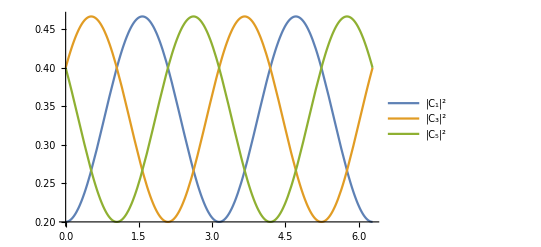

```mathematica
Plot[{C1m*Conjugate[C1m], C3m * Conjugate[C3m], C5m * Conjugate[C5m]}, {θ, 0, 2 π}, PlotLegends->{"|C_1|^2","|C_3|^2", "|C_5|^2" }]
```

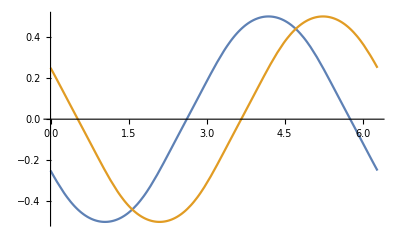

```mathematica
Plot[{Arg[C3m/C1m]*1/π,Arg[C5m/C1m]*1/π}, {θ, 0, 2 π}]
```

```mathematica
Clear[α, q, Δ, θ]
```

```mathematica
Series[FullSimplify[ComplexExpand[Conjugate[C1m]*C1m]], {q, 0, 2}]
```

1/3-(2 (α^2 Cos[2 θ]) q^2)/(9 Δ^2)+O[q]^3

```mathematica
Series[FullSimplify[ComplexExpand[Conjugate[C3m]*C3m]], {q, 0, 2}]
```

1/3+((α^2 Cos[2 θ]+√3 α^2 Sin[2 θ]) q^2)/(9 Δ^2)+O[q]^3

```mathematica
Series[FullSimplify[ComplexExpand[Conjugate[C5m]*C5m]], {q, 0, 2}]
```

1/3+((α^2 Cos[2 θ]-√3 α^2 Sin[2 θ]) q^2)/(9 Δ^2)+O[q]^3

```mathematica
FullSimplify[D[C5m, θ]]
```

-(ⅈ (2 √6 q α+3 Δ+√(24 q^2 α^2+9 Δ^2)) (√3 Cos[θ]+3 Sin[θ]))/(6 √6 √(3 Δ^2+2 q α (4 q α+√(16 q^2 α^2+6 Δ^2))))

```mathematica
FullSimplify[Re[Conjugate[C5m]*D[C5m, q]]]
```

-(q α^2 Δ (√3 Cos[2 θ]-3 Sin[2 θ]))/(3 (8 q^2 α^2+3 Δ^2)^(3/2))

```mathematica
FullSimplify[Re[Conjugate[C1m]*D[C1m, θ]]]
```

1/3 (1+(√3 Δ)/(√(8 q^2 α^2+3 Δ^2))) Cos[θ] Sin[θ]

```mathematica
FullSimplify[Re[Conjugate[C3m]*D[C3m, θ]]]
```

1/12 ((√3+(3 Δ)/(√(8 q^2 α^2+3 Δ^2))) Cos[2 θ]+(-1-(√3 Δ)/(√(8 q^2 α^2+3 Δ^2))) Sin[2 θ])

```mathematica
FullSimplify[Re[Conjugate[C5m]*D[C5m, θ]]]
```

1/12 (-Sin[2 θ]+(-((3 Δ+√(24 q^2 α^2+9 Δ^2)) Cos[2 θ])-√3 Δ Sin[2 θ])/(√(8 q^2 α^2+3 Δ^2)))

## Useful Checks

```mathematica
θ = ArcTan[x,y]
q=Sqrt[x^2+y^2]
```

ArcTan[x,y]

√(x^2+y^2)

```mathematica
Δ=-1
α=2
```

-1

2

```mathematica
FullSimplify[C1m]
```

(√(2/3) x)/(√(x^2+y^2))

```mathematica
C1[x_,y_]:=(4 √3 √(x^2+y^2) α-3 √2 Δ+√(48 (x^2+y^2) α^2+18 Δ^2)+(2 ⅈ y (2 √6 √(x^2+y^2) α+3 Δ+√(24 (x^2+y^2) α^2+9 Δ^2)))/(√(x^2+y^2)))/(6 √(6 Δ^2+4 α (4 (x^2+y^2) α+√2 √((x^2+y^2) (8 (x^2+y^2) α^2+3 Δ^2)))))
```

```mathematica
C3[x_,y_]:=(-3 (3 ⅈ x+ⅈ √3 y+√6 √(x^2+y^2)) Δ-2 (3 ⅈ x+ⅈ √3 y-√6 √(x^2+y^2)) (√6 √(x^2+y^2) α+√(6 (x^2+y^2) α^2+(9 Δ^2)/4)))/(12 √((x^2+y^2) ((9 Δ^2)/2+3 √(x^2+y^2) α (4 √(x^2+y^2) α+√(16 (x^2+y^2) α^2+6 Δ^2)))))
```

```mathematica
C5[x_,y_]:=(-3 (-3 ⅈ x+ⅈ √3 y+√6 √(x^2+y^2)) Δ+2 (3 ⅈ x-ⅈ √3 y+√6 √(x^2+y^2)) (√6 √(x^2+y^2) α+√(6 (x^2+y^2) α^2+(9 Δ^2)/4)))/(12 √((x^2+y^2) ((9 Δ^2)/2+3 √(x^2+y^2) α (4 √(x^2+y^2) α+√(16 (x^2+y^2) α^2+6 Δ^2)))))
```

```mathematica
temp1 = Im[Conjugate[D[C1[x,y],x]] * D[C1[x,y],y]] + Im[Conjugate[D[C3[x,y],x]] * D[C3[x,y],y]] + Im[Conjugate[D[C5[x,y],x]] * D[C5[x,y],y]]
```

Im[(((8 √3 y)/(√(x^2+y^2))+(192 y)/(√(18+192 (x^2+y^2)))+(2 ⅈ y ((4 √6 y)/(√(x^2+y^2))+(96 y)/(√(9+96 (x^2+y^2)))))/(√(x^2+y^2))-(2 ⅈ y^2 (-3+4 √6 √(x^2+y^2)+√(9+96 (x^2+y^2))))/((x^2+y^2)^(3/2))+(2 ⅈ (-3+4 √6 √(x^2+y^2)+√(9+96 (x^2+y^2))))/(√(x^2+y^2)))/(6 √(6+8 (8 (x^2+y^2)+√2 √((x^2+y^2) (3+32 (x^2+y^2))))))-(2 (16 y+(64 y (x^2+y^2)+2 y (3+32 (x^2+y^2)))/(√2 √((x^2+y^2) (3+32 (x^2+y^2))))) (3 √2+8 √3 √(x^2+y^2)+√(18+192 (x^2+y^2))+(2 ⅈ y (-3+4 √6 √(x^2+y^2)+√(9+96 (x^2+y^2))))/(√(x^2+y^2))))/(3 (6+8 (8 (x^2+y^2)+√2 √((x^2+y^2) (3+32 (x^2+y^2)))))^(3/2))) Conjugate[((8 √3 x)/(√(x^2+y^2))+(192 x)/(√(18+192 (x^2+y^2)))+(2 ⅈ y ((4 √6 x)/(√(x^2+y^2))+(96 x)/(√(9+96 (x^2+y^2)))))/(√(x^2+y^2))-(2 ⅈ x y (-3+4 √6 √(x^2+y^2)+√(9+96 (x^2+y^2))))/((x^2+y^2)^(3/2)))/(6 √(6+8 (8 (x^2+y^2)+√2 √((x^2+y^2) (3+32 (x^2+y^2))))))-(2 (16 x+(64 x (x^2+y^2)+2 x (3+32 (x^2+y^2)))/(√2 √((x^2+y^2) (3+32 (x^2+y^2))))) (3 √2+8 √3 √(x^2+y^2)+√(18+192 (x^2+y^2))+(2 ⅈ y (-3+4 √6 √(x^2+y^2)+√(9+96 (x^2+y^2))))/(√(x^2+y^2))))/(3 (6+8 (8 (x^2+y^2)+√2 √((x^2+y^2) (3+32 (x^2+y^2)))))^(3/2))]]+Im[((3 (ⅈ √3+(√6 y)/(√(x^2+y^2)))-2 (3 ⅈ x+ⅈ √3 y-√6 √(x^2+y^2)) ((2 √6 y)/(√(x^2+y^2))+(24 y)/(√(9/4+24 (x^2+y^2))))-2 (ⅈ √3-(√6 y)/(√(x^2+y^2))) (2 √6 √(x^2+y^2)+√(9/4+24 (x^2+y^2))))/(12 √((x^2+y^2) (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))))-((3 (3 ⅈ x+ⅈ √3 y+√6 √(x^2+y^2))-2 (3 ⅈ x+ⅈ √3 y-√6 √(x^2+y^2)) (2 √6 √(x^2+y^2)+√(9/4+24 (x^2+y^2)))) ((x^2+y^2) (6 √(x^2+y^2) ((8 y)/(√(x^2+y^2))+(64 y)/(√(6+64 (x^2+y^2))))+(6 y (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))/(√(x^2+y^2)))+2 y (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))))/(24 ((x^2+y^2) (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2)))))^(3/2))) Conjugate[(3 (3 ⅈ+(√6 x)/(√(x^2+y^2)))-2 (3 ⅈ x+ⅈ √3 y-√6 √(x^2+y^2)) ((2 √6 x)/(√(x^2+y^2))+(24 x)/(√(9/4+24 (x^2+y^2))))-2 (3 ⅈ-(√6 x)/(√(x^2+y^2))) (2 √6 √(x^2+y^2)+√(9/4+24 (x^2+y^2))))/(12 √((x^2+y^2) (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))))-((3 (3 ⅈ x+ⅈ √3 y+√6 √(x^2+y^2))-2 (3 ⅈ x+ⅈ √3 y-√6 √(x^2+y^2)) (2 √6 √(x^2+y^2)+√(9/4+24 (x^2+y^2)))) ((x^2+y^2) (6 √(x^2+y^2) ((8 x)/(√(x^2+y^2))+(64 x)/(√(6+64 (x^2+y^2))))+(6 x (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))/(√(x^2+y^2)))+2 x (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))))/(24 ((x^2+y^2) (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2)))))^(3/2))]]+Im[((3 (ⅈ √3+(√6 y)/(√(x^2+y^2)))+2 (3 ⅈ x-ⅈ √3 y+√6 √(x^2+y^2)) ((2 √6 y)/(√(x^2+y^2))+(24 y)/(√(9/4+24 (x^2+y^2))))+2 (-ⅈ √3+(√6 y)/(√(x^2+y^2))) (2 √6 √(x^2+y^2)+√(9/4+24 (x^2+y^2))))/(12 √((x^2+y^2) (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))))-((3 (-3 ⅈ x+ⅈ √3 y+√6 √(x^2+y^2))+2 (3 ⅈ x-ⅈ √3 y+√6 √(x^2+y^2)) (2 √6 √(x^2+y^2)+√(9/4+24 (x^2+y^2)))) ((x^2+y^2) (6 √(x^2+y^2) ((8 y)/(√(x^2+y^2))+(64 y)/(√(6+64 (x^2+y^2))))+(6 y (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))/(√(x^2+y^2)))+2 y (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))))/(24 ((x^2+y^2) (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2)))))^(3/2))) Conjugate[(3 (-3 ⅈ+(√6 x)/(√(x^2+y^2)))+2 (3 ⅈ x-ⅈ √3 y+√6 √(x^2+y^2)) ((2 √6 x)/(√(x^2+y^2))+(24 x)/(√(9/4+24 (x^2+y^2))))+2 (3 ⅈ+(√6 x)/(√(x^2+y^2))) (2 √6 √(x^2+y^2)+√(9/4+24 (x^2+y^2))))/(12 √((x^2+y^2) (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))))-((3 (-3 ⅈ x+ⅈ √3 y+√6 √(x^2+y^2))+2 (3 ⅈ x-ⅈ √3 y+√6 √(x^2+y^2)) (2 √6 √(x^2+y^2)+√(9/4+24 (x^2+y^2)))) ((x^2+y^2) (6 √(x^2+y^2) ((8 x)/(√(x^2+y^2))+(64 x)/(√(6+64 (x^2+y^2))))+(6 x (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))/(√(x^2+y^2)))+2 x (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2))))))/(24 ((x^2+y^2) (9/2+6 √(x^2+y^2) (8 √(x^2+y^2)+√(6+64 (x^2+y^2)))))^(3/2))]]

```mathematica
x = 0
y =0
FullSimplify[temp1]
```

0

0

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √3 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

Indeterminate

```mathematica
Clear[x,y]
```